# Condutor Equivalente para Feixes de Condutores

## Antonio Carlos Siqueira de Lima Outubro 2021

## Circuito Convencional 345 kV

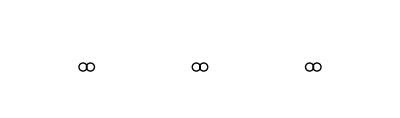

```mathematica
(*
xy1 = {{-7.229, 10.5}, {-6.771, 10.500}, {-0.229, 10.500}, {0.229, 
    10.500}, {7.229, 10.500},
   {6.771, 10.500}, {-5.000, 20.500}, {5.000, 20.500}};
*)
xy1 = {{-7.229, 10.5}, {-6.771, 10.500}, {-0.229, 10.500}, {0.229, 
    10.500}, {7.229, 10.500},
   {6.771, 10.500}};

mostra1 = {Circle[#, .25]} & /@ xy1;

t1 = Show[Graphics[mostra1], AspectRatio -> Automatic, Axes -> False, 
  Frame -> Automatic, PlotRange -> {{-10.1, 10.1}, {8,14}}, 
  FrameLabel -> {"distância (m)", "distância (m)"}]
```

```mathematica
xc=xy1[[All,1]];
```

```mathematica
yc=xy1[[All,2]];
```

```mathematica
(* mostra=Table[{Circle[{xc[[i]],yc[[i]]},0.5]},{i,1,3}];
tduplo=Show[Graphics[mostra],AspectRatio->Automatic,Axes->False,Frame->Automatic,PlotRange->{{-12,12},{0,28}},FrameLabel->{"distância (m)","distância (m)"}]*)
```

```mathematica
rf=4.06908/2 10^-2;
```

```mathematica
Aux[rf_,x_:xc,y_:yc]:=Table[If[i≠j,1/2Log[((x[[i]]-x[[j]])^2+(y[[i]]+y[[j]])^2)/((x[[i]]-x[[j]])^2+(y[[i]]-y[[j]])^2)],
Log[2 y[[i]]/rf]],{i,1,Length[x]},{j,1,Length[x]}]
```

```mathematica
pot=Aux[rf,xc,yc];
MatrixForm[pot]
```

(6.93942 | 3.82565 | 1.15129 | 1.09463 | 0.567264 | 0.589327
3.82565 | 6.93942 | 1.21259 | 1.15129 | 0.589327 | 0.612588
1.15129 | 1.21259 | 6.93942 | 3.82565 | 1.09463 | 1.15129
1.09463 | 1.15129 | 3.82565 | 6.93942 | 1.15129 | 1.21259
0.567264 | 0.589327 | 1.09463 | 1.15129 | 6.93942 | 3.82565
0.589327 | 0.612588 | 1.15129 | 1.21259 | 3.82565 | 6.93942)

```mathematica
(*  reduce bundle to equivalent phase conductors -- matrizes devem estar em formato de admitancia *)
elibndc = Compile[{{aux,_Complex,2},{nb,_Integer},{nf,_Integer}},
	          Table[Sum[aux[[i, j]], {i, nb*m - (nb - 1), nb*m}, {j, nb*n - (nb - 1), nb*n}],
                       {m, nf},{n, nf}]
                 ]
```

CompiledFunction[…]

```mathematica
invpot=Inverse@pot;
```

```mathematica
MatrixForm[c1=elibndc[invpot, 2, 3]]
```

(0.19561+0. ⅈ | -0.0390814+0. ⅈ | -0.0130837+0. ⅈ
-0.0390814+0. ⅈ | 0.20256+0. ⅈ | -0.0390814+0. ⅈ
-0.0130837+0. ⅈ | -0.0390814+0. ⅈ | 0.19561+0. ⅈ)

```mathematica
Dimensions[c1]
```

{3,3}

```mathematica
cs=Re@Tr[c1]/3;
cm=Re@(c1[[1,2]]+c1[[1,3]]+c1[[2,3]])/3;
```

```mathematica
MatrixForm[ctransp= Table[If[i≠ j, cm, cs],{i,3},{j,3}]]
```

(0.197927 | -0.0304155 | -0.0304155
-0.0304155 | 0.197927 | -0.0304155
-0.0304155 | -0.0304155 | 0.197927)

```mathematica
a=Exp[ⅉ 120 Degree];
```

```mathematica
MatrixForm[A={{1,1,1},{1,a ^2, a},{1,a,a^ 2}}]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
MatrixForm[C012=Inverse[A].ctransp.A//Chop]
```

(0.137096 | 0 | 0
0 | 0.228342 | 0
0 | 0 | 0.228342)

```mathematica
cs-cm
```

0.228342

```mathematica
cs+2cm
```

0.137096

## Utilizando a fórmula

c_1=2π ϵ 1/(Log(DMG/RMG hmg/HMG))
DM G - distância média entre os condutores,
RMG - raio médio geométrico dos condutores de fase
 hmg  - distância média geométrica entre condutores em relação às imagens de mesma fase
 HMG - dos condutores em relação às imagens de condutores de outras

```mathematica
xcb=.5{xc[[1]]+xc[[2]], xc[[3]]+xc[[4]], xc[[5]]+xc[[6]]}
```

{-7.,0.,7.}

```mathematica
ycb=.5{yc[[1]]+yc[[2]], yc[[3]]+yc[[4]], yc[[5]]+yc[[6]]}
```

{10.5,10.5,10.5}

```mathematica
rfeixe=0.229;
```

```mathematica
RMG=Sqrt[rf 2 rfeixe]
```

0.0965308

```mathematica
HMG=(2ycb [[1]] 2ycb[[2]] 2ycb[[3]])^(1/3)
```

21.

```mathematica
hmg=(ycb [[1]]ycb[[2]] ycb[[3]])^(1/3)
```

10.5

```mathematica
DMG =(Sqrt[(xcb[[1]] - xcb[[2]])^2+()])^(1/3)
```